```mathematica
(*ML Data*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLF1MathematicaReads.xlsx"];
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

84

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

84

```mathematica
(*fitting to 90% of the data*)
n90=Floor[nΔYVec (0.9)]
```

75

```mathematica
(*Covariates*)


(*Yield Curve*)
X1Vec=Data[[1,All,3]];

(*Norfarm Jobs*)
X2Vec=Data[[1,All,4]];

(*Federal Funds*)
X3Vec=Data[[1,All,5]];

(*Mortgage Rate*)
X4Vec=Data[[1,All,6]];

(*Personal Consumption Expeditures*)
X5Vec=Data[[1,All,7]];

(*Industrial Production*)
X6Vec=Data[[1,All,8]];

(*Consumer Price Index*)
X7Vec=Data[[1,All,9]];

(*Crude Oil Prices*)
X8Vec=Data[[1,All,10]];

(*NASDAQ Composite Index*)
X9Vec=Data[[1,All,11]];
```

```mathematica
(*Plot Y - Observed data*)
```

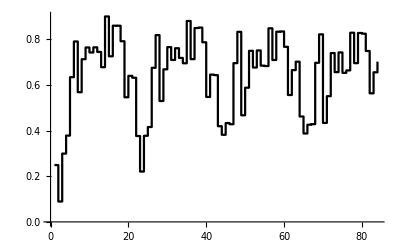

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Black]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=3)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 YVec[[i-1]] +β8 X1[[i-1]]+β9 X2[[i-1]]+β10 X3[[i-1]]+β11 X4[[i-1]]  +β14 YVec[[i-2]] +β15 X1[[i-2]]+β16 X2[[i-2]]+β17 X3[[i-2]]+β18 X4[[i-2]] ))/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];
Dβ4=Simplify[D[LnL,β4]];


Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];
Dβ9=Simplify[D[LnL,β9]];
Dβ10=Simplify[D[LnL,β10]];
Dβ11=Simplify[D[LnL,β11]];


Dβ14=Simplify[D[LnL,β14]];
Dβ15=Simplify[D[LnL,β15]];
Dβ16=Simplify[D[LnL,β16]];
Dβ17=Simplify[D[LnL,β17]];
Dβ18=Simplify[D[LnL,β18]];


Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ7},{0==Dβ8},{0==Dβ9},{0==Dβ10},{0==Dβ11},{0==Dβ14},{0==Dβ15},{0==Dβ16},{0==Dβ17},{0==Dβ18},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β7,0.1},{β8,0.1},{β9,0.1},{β10,0.1},{β11,0.1},{β14,0.1},{β15,0.1},{β16,0.1},{β17,0.1},{β18,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦3⟧ is longer than depth of object.

Part::partd: Part specification X2⟦3⟧ is longer than depth of object.

Part::partd: Part specification X3⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→-10.8219,β1→0.116568,β2→0.0100854,β3→-0.0230429,β4→0.0000306254,β7→-0.783615,β8→0.00345295,β9→-0.0049449,β10→0.0149055,β11→-0.000112736,β14→-0.0319364,β15→0.00250986,β16→0.0086447,β17→-0.0258191,β18→-0.0000609024,σ→1.03334×10^103}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 YVec[[i-1]] +β8 X1[[i-1]]+β9 X2[[i-1]]+β10 X3[[i-1]]+β11 X4[[i-1]]+β14 YVec[[i-2]] +β15 X1[[i-2]]+β16 X2[[i-2]]+β17 X3[[i-2]]+β18 X4[[i-2]];
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]],ΔYVec[[2]]};
For[k=3,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression -2+i cannot be used as a part specification.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

{0.,-0.159757,0.251931,0.112629,0.232252,0.197746,-0.240568,0.143141,0.0474313,-0.0519565,-0.0362313,-0.0546059,-0.0668001,0.209447,-0.224863,0.0762207,0.0102502,-0.0724197,-0.191909,0.0473052,0.0356665,-0.252665,-0.0209858,0.144875,0.0471469,0.200255,0.164277,-0.263813,0.172562,0.0833832,-0.0518212,-0.0105867,-0.0505169,-0.0459651,0.196758,-0.209828,0.0866048,0.0187307,-0.0656767,-0.188131,0.0463576,0.0313621,-0.261882,-0.0549519,0.0172817,-0.00158652,0.189015,0.147962,-0.275661,0.221127,0.148518,-0.0364697,0.0159492,-0.0418443,-0.0192233,0.207406,-0.184325,0.0905669,0.0315489,-0.0518768,-0.171906,0.0402863,0.0156586,-0.308616,-0.0902033,0.0114058,0.00387185,0.188911,0.146761,-0.267095,0.247702,0.178715,-0.0277156,0.0320452,-0.0344073,0.00585514,0.223369,-0.168549,0.102024,0.0362876,-0.0440814,-0.157313,0.0351441,0.0229476}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.249077,0.0893193,0.341251,0.453879,0.686131,0.883877,0.643309,0.78645,0.833882,0.781925,0.745694,0.691088,0.624288,0.833735,0.608871,0.685092,0.695342,0.622923,0.431014,0.478319,0.513986,0.261321,0.240335,0.38521,0.432357,0.632612,0.796889,0.533076,0.705638,0.789021,0.7372,0.726613,0.676096,0.630131,0.82689,0.617061,0.703666,0.722397,0.65672,0.468589,0.514947,0.546309,0.284427,0.229475,0.246757,0.24517,0.434185,0.582147,0.306486,0.527613,0.676131,0.639661,0.65561,0.613766,0.594543,0.801949,0.617624,0.708191,0.73974,0.687863,0.515957,0.556243,0.571902,0.263286,0.173083,0.184488,0.18836,0.377271,0.524033,0.256937,0.504639,0.683353,0.655638,0.687683,0.653276,0.659131,0.8825,0.713951,0.815975,0.852262,0.808181,0.650868,0.686012,0.70896}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.249077},{2,0.0893193},{3,0.341251},{4,0.453879},{5,0.686131},{6,0.883877},{7,0.643309},{8,0.78645},{9,0.833882},{10,0.781925},{11,0.745694},{12,0.691088},{13,0.624288},{14,0.833735},{15,0.608871},{16,0.685092},{17,0.695342},{18,0.622923},{19,0.431014},{20,0.478319},{21,0.513986},{22,0.261321},{23,0.240335},{24,0.38521},{25,0.432357},{26,0.632612},{27,0.796889},{28,0.533076},{29,0.705638},{30,0.789021},{31,0.7372},{32,0.726613},{33,0.676096},{34,0.630131},{35,0.82689},{36,0.617061},{37,0.703666},{38,0.722397},{39,0.65672},{40,0.468589},{41,0.514947},{42,0.546309},{43,0.284427},{44,0.229475},{45,0.246757},{46,0.24517},{47,0.434185},{48,0.582147},{49,0.306486},{50,0.527613},{51,0.676131},{52,0.639661},{53,0.65561},{54,0.613766},{55,0.594543},{56,0.801949},{57,0.617624},{58,0.708191},{59,0.73974},{60,0.687863},{61,0.515957},{62,0.556243},{63,0.571902},{64,0.263286},{65,0.173083},{66,0.184488},{67,0.18836},{68,0.377271},{69,0.524033},{70,0.256937},{71,0.504639},{72,0.683353},{73,0.655638},{74,0.687683},{75,0.653276},{76,0.659131},{77,0.8825},{78,0.713951},{79,0.815975},{80,0.852262},{81,0.808181},{82,0.650868},{83,0.686012},{84,0.70896}}

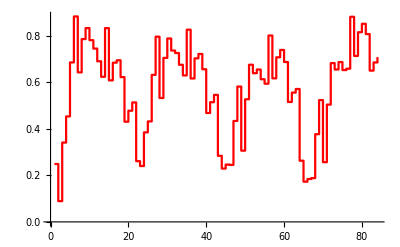

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->0, Joined->True,PlotStyle->Red,PlotRange->All]
```

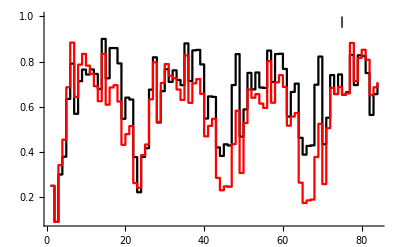

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)

A=Show[{YObserved,YPredictedPlotInt},Graphics[{Black, Line[{{n90,0.95},{n90,1}}]}],PlotRange->All]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

1.14673

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0161482

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

0.00161482

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->6
```

0.327591